```mathematica
b=2;
c=3/2;
fitO := o + (b-c)*y + b*B;
fitY := (b-cO)*o + y + (b-cB)*B;
fitB := o*(b-c) + b*y + B;

fitmedio := fitO * o + fitY * y + fitB * B;

dodt := o * (fitO - fitmedio);
dydt := y * (fitY - fitmedio);
dbdt := B * (fitB - fitmedio);

equilibrio = Solve[{dodt == 0 && dydt == 0 && dbdt == 0, o + y + B ==1}, {o, y, B}]
jacobiana=FullSimplify[D[{dodt,dydt,dbdt},{{o,y,B}}]];
MatrixForm[jacobiana]
```

{{o→1,y→0,B→0},{o→0,y→0,B→1},{o→2,y→0,B→-1},{o→0,y→1,B→0},{o→0,y→(-1+cB)/(-2+cB),B→1/(2-cB)},{o→(2 (-1+3 cB))/(9+8 cB-10 cO),y→(2 (2+cB-2 cO))/(9+8 cB-10 cO),B→(7-6 cO)/(9+8 cB-10 cO)},{o→1/(-1+2 cO),y→(2 (-1+cO))/(-1+2 cO),B→0}}

(-B^2-3 o^2+1/2 (1-2 y) y+B (2-5 o+(-4+cB) y)+o (2-5 y+2 cO y) | 1/2 o (1+2 B (-4+cB)+(-5+2 cO) o-4 y) | -1/2 o (-4+4 B+5 o+8 y-2 cB y)
-1/2 y (-4+5 B+4 o-2 cO (-1+y)+5 y) | -B^2-o (-2+cO+o)+(2+(-5+2 cO) o) y-3 y^2+B (2-(5 o)/2-8 y+cB (-1+2 y)) | -1/2 y (-4+4 B+5 o-2 cB (-1+y)+8 y)
-1/2 B (-1+5 B+4 o+5 y-2 cO y) | 1/2 B (4+2 B (-4+cB)+(-5+2 cO) o-4 y) | -3 B^2+B (2-5 o+2 (-4+cB) y)+1/2 (o-2 o^2+(-5+2 cO) o y-2 (-2+y) y))

```mathematica
equilibrio[[1]]
mat1=jacobiana/. equilibrio[[1]];
autovalores1=Eigenvalues[mat1]
Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0&& Max[Re[autovalores1]]<0]]
```

{o→1,y→0,B→0}

{-1,-1/2,1-cO}

True

```mathematica
equilibrio[[2]]
mat2=jacobiana/. equilibrio[[2]];
autovalores2=Eigenvalues[mat2]
Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0&& Max[Re[autovalores2]]<0]]
```

{o→0,y→0,B→1}

{-1,1,1-cB}

False

```mathematica
equilibrio[[3]]
mat3=jacobiana/. equilibrio[[3]];
autovalores3=Eigenvalues[mat3]
Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0 && Max[Re[autovalores3]]<0]]
```

{o→2,y→0,B→-1}

{1,0,2+cB-2 cO}

False

```mathematica
equilibrio[[4]]
mat4=jacobiana/. equilibrio[[4]];
autovalores4=Eigenvalues[mat4]
Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0&& Max[Re[autovalores4]]<0]]
```

{o→0,y→1,B→0}

{-1,1,-1/2}

False

```mathematica
equilibrio[[6]]
mat6=jacobiana/. equilibrio[[6]];
autovalores6=Eigenvalues[mat6]
Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0&& 0<=(2 (-1+3 cB))/(9+8 cB-10 cO)<=1 && 0<=(2 (2+cB-2 cO))/(9+8 cB-10 cO)<=1 && 0<= (7-6 cO)/(9+8 cB-10 cO) <=1 &&Max[Re[autovalores6]]<0]]
```

{o→(2 (-1+3 cB))/(9+8 cB-10 cO),y→(2 (2+cB-2 cO))/(9+8 cB-10 cO),B→(7-6 cO)/(9+8 cB-10 cO)}

{-(7 (18+25 cB+8 cB^2-38 cO-26 cB cO+20 cO^2))/(9+8 cB-10 cO)^2,(-45-31 cB+8 cB^2+86 cO+22 cB cO-40 cO^2-(9+8 cB-10 cO) √(81-150 cB-83 cB^2-144 cO+296 cB cO+72 cB^2 cO+64 cO^2-144 cB cO^2))/(2 (9+8 cB-10 cO)^2),(-45-31 cB+8 cB^2+86 cO+22 cB cO-40 cO^2+(9+8 cB-10 cO) √(81-150 cB-83 cB^2-144 cO+296 cB cO+72 cB^2 cO+64 cO^2-144 cB cO^2))/(2 (9+8 cB-10 cO)^2)}

True

```mathematica
equilibrio[[7]]
mat7=jacobiana/. equilibrio[[7]];
autovalores7=Eigenvalues[mat7]
Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0 && 0<= 1/(-1+2 cO)<=1 && 0<=(2 (-1+cO))/(-1+2 cO)<=1&& Max[Re[autovalores7]]<0]]
```

{o→1/(-1+2 cO),y→(2 (-1+cO))/(-1+2 cO),B→0}

{(-7+6 cO)/(2 (-1+2 cO)),(1-3 cO+2 cO^2)/(-1+2 cO)^2,-(-cO+2 cO^2)/(-1+2 cO)^2}

False

```mathematica
equilibrio[[5]]
mat5=jacobiana/. equilibrio[[5]];
autovalores5=Eigenvalues[mat5]
Resolve[Exists[{cO, cB}, cO <= cB && cO >=0 && cB>=0 &&0<=(-1+cB)/(-2+cB)<=1 && 0<=1/(2-cB)<=1 &&  Max[Re[autovalores5]]<0]]
```

{o→0,y→(-1+cB)/(-2+cB),B→1/(2-cB)}

{-(-1+3 cB)/(2 (-2+cB)),-(2-3 cB+cB^2)/(-2+cB)^2,-(6-7 cB+2 cB^2)/(-2+cB)^2}

True

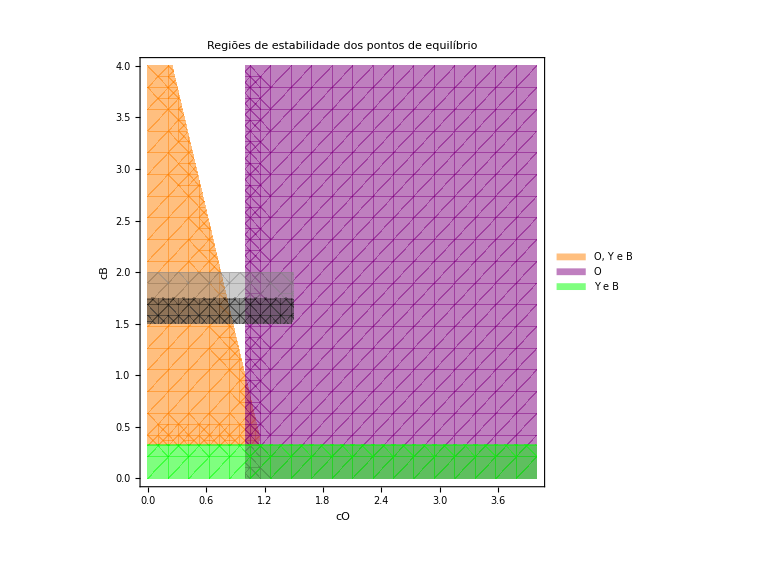

```mathematica
rO= Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0&& Max[Re[autovalores1]]<0]];
r3 = Resolve[Exists[{cO, cB},cO <= cB && cO >=0 && cB>=0&& 0<=(2 (-1+3 cB))/(9+8 cB-10 cO)<=1 && 0<=(2 (2+cB-2 cO))/(9+8 cB-10 cO)<=1 && 0<= (7-6 cO)/(9+8 cB-10 cO) <=1 &&Max[Re[autovalores6]]<0]];
rYB = Resolve[Exists[{cO, cB}, cO <= cB && cO >=0 && cB>=0 &&0<=(-1+cB)/(-2+cB)<=1 && 0<=1/(2-cB)<=1 &&  Max[Re[autovalores5]]<0]];
plotO = RegionPlot[cO >=0 && cB>=0&& Max[Re[autovalores1]]<0,
{cO,0,4},{cB,0,4},
PlotStyle->{Purple,Opacity[0.5]},
BoundaryStyle->None,
PlotLegends->Placed[{"O"},Below]];

plot3 = RegionPlot[cO >=0 && cB>=0&& 0<=(2 (-1+3 cB))/(9+8 cB-10 cO)<=1 && 0<=(2 (2+cB-2 cO))/(9+8 cB-10 cO)<=1 && 0<= (7-6 cO)/(9+8 cB-10 cO) <=1 &&Max[Re[autovalores6]]<0,
{cO,0,4},{cB,0,4},
PlotStyle->{Orange,Opacity[0.5]},
BoundaryStyle->None,
PlotLegends->Placed[{"O, Y e B"},Below]];

plotYB = RegionPlot[cO >=0 && cB>=0 &&0<=(-1+cB)/(-2+cB)<=1 && 0<=1/(2-cB)<=1 &&  Max[Re[autovalores5]]<0,
{cO,0,4},{cB,0,4},
PlotStyle->{Green,Opacity[0.5]},
BoundaryStyle->None,
PlotLegends->Placed[{"Y e B"},Below]];
regiao=RegionPlot[0<=cO<=1.5&&1.5<=cB<=2,{cO,0,4},{cB,0,4},PlotStyle->{Opacity[0.4],Gray},BoundaryStyle->None];
regiao1=RegionPlot[0<=cO<=1.5&&1.5<=cB<=1.75,{cO,0,4},{cB,0,4},PlotStyle->{Opacity[0.3],Black},BoundaryStyle->None];

Show[plot3, plotO,plotYB, regiao,regiao1, FrameLabel->{"cO","cB"},PlotLabel->"Regiões de estabilidade dos pontos de equilíbrio",ImageSize->Large, Method->{"TransparentPolygonMesh"->True}]
```